### ΔN_eff Early Universe with Hubble

To run simply evaluate the entire notebook SM Early Universe and look at Results

#### Documentation

The code is based upon the fact that non-thermal equilibrium corrections to the neutrino distribution functions are small. And actually, a thermal distribution function with evolving temperature ,Tν can account for the number and energy density of neutrinos very accurately. 

The result in terms of Neff in the SM is: Neff = 3.046. This is in excellent agreement with state-of-the-art calculations in the SM 1606.06986, hep-ph/0506164. In my computer the programm takes ~25 seconds to run. 

The code has 4 sections.
	1-Finite Temperature Corrections: Loads the finite temperature corrections to the electromagnetic energy and pressure densities from 1 loop QED.
	2-SM Neutrino interactions with me: Loads the SM neutrino-electron and neutrino-neutrino number and energy exchanges rates. They include the effect of the electron mass. 
	3-Thermodynamics and Expansion: Defines the relevant number, energy and pressure densities for electrons, photons and neutrinos. 
	4-Temperature ODE: Defines the time evolution equations for zγ ≡ a Tγ/m_e, and zν ≡ a Tν/m_e.
	5-Key function. Solves zγ(a) and zν(a) as well as Tγ(t) and Tν(t),

The function ΔNeffND[Tν0_,ΔNeff_] is the key one. You need to enter the starting temperature, which I recommend to be 20 MeV, and the given ΔNeff. Note that only positive values are allowed.
It outputs a vector containing: 
	1 Neff
	2 the asymtotic value of zγ
	3 the asymtotic value of zν
	4 zγ(a)
	5 zν(a)
	6 N(a)
	7 Mpl H/Tγ^2 (a), Mpl = 1.2209 10^19 10^3 MeV
	8 a(Tγ in MeV)
	9 a(t in seconds)
	10 Tγ(a)   in MeV
	11 Tγ(t in seconds) in MeV
	12 Tν/Tγ(t in seconds) 
	13 Tν/Tγ(Tγ in MeV)
	14 Mpl H/Tγ^2 (t in seconds), Mpl = 1.2209 10^19 10^3 MeV
zγ(a), zν(a)  are defined in Equation 28 of 1801.08023 and N(a) is defined in eq 60 of 1801.08023. PRIMAT uses both. 

The code is based on arXiv:1812.05605 but uses updated neutrino-neutrino and neutrino electron rates from arXiv:1907.XXXXX. All dimensionfull variables are in MeV.

#### Comments about ΔN_eff

We can easily compute the early Universe evolution when additional massless and non-interacting species contribute to radiation at the time of BBN. We can use entropy conservation to know what is the initial ratio of temperatures T_α/T_γ at T = 20 MeV, corresponds to a given ΔN_eff ensures that at temperatures T > 10 MeV:

For a scalar boson, α, the relationship at, T ≥ 10 MeV, between the temperatures can be expressed as:

T_α/T_γ = (2^(1/6) 7^(1/4) gSMi^(1/3)  ΔΔNeff^(1/4))/(11^(1/3) gSMf^(1/3))

where in gSMi = 10.75, and gSMf =  3.933.

```mathematica
(*sSMi =  T0^3 gSMi;
sDRi =  T0DR^3 gDRi;

sSMf =  TSMf^3 gSMf;
sDRf =  TDRf^3 gDRi;

Solve[sDRf/(sDRf+sSMf)==sDRi/(sDRi+sSMi),{TDRf}]
ΔNeff =8/7(11/4)^(4/3)((π^2/30 TDRf^4)/(2 π^2/30 TSMf^4) );
Solve[ΔΔNeff== ΔNeff/.{TDRf->(gSMf^(1/3) T0DR TSMf)/(gSMi^(1/3) T0)},T0DR]*)
```

#### 1-Finite Temperature Corrections

```mathematica
SetDirectory[NotebookDirectory[]];
mgdata=Import["QED_MEV/QED_P_int.cvs","Table",HeaderLines-> 1];
mgPint=Interpolation[mgdata];
mgdata2=Import["QED_MEV/QED_dP_intdT.cvs","Table",HeaderLines-> 1];
mgdPintdT:=Interpolation[mgdata2];
mgdata3=Import["QED_MEV/QED_d2P_intdT2.cvs","Table",HeaderLines-> 1];
mgd2PintdT2:=Interpolation[mgdata3];
```

#### 2-SM Neutrino interactions with me

```mathematica
SetDirectory[NotebookDirectory[]];
mgdata=Import["Rate_MeV/nue_ann.dat","Table",HeaderLines-> 1];
mgfannνe=Interpolation[mgdata];

mgdata=Import["Rate_MeV/nue_scatt.dat","Table",HeaderLines-> 1];
mgfscaνe=Interpolation[mgdata];

mgdata=Import["Rate_MeV/numu_ann.dat","Table",HeaderLines-> 1];
mgfannνμ=Interpolation[mgdata];

mgdata=Import["Rate_MeV/numu_scatt.dat","Table",HeaderLines-> 1];
mgfscaνμ=Interpolation[mgdata];

mgFunc[T1_,T2_]:=32 0.884*(T1^9-T2^9)+56 T1^4 T2^4*0.829*(T1-T2);

mgΔρSMνe[Tγ_,Tνe_,Tνμ_]:=  mgGF^2/π^5((1+4 mgSW2 +8 mgSW2^2)(32 0.884*mgfannνe[Tγ]*(Tγ^9-Tνe^9)+56 Tγ^4 *mgfscaνe[Tγ]*Tνe^4*0.829*(Tγ-Tνe))+2mgFunc[Tνμ,Tνe])/.{mgSW2-> 0.223}/.mgGF-> 1.1663787 10^-11;
mgΔρSMνμ[Tγ_,Tνe_,Tνμ_]:=  mgGF^2/π^5((1-4 mgSW2 +8 mgSW2^2)(32 0.884*mgfannνμ[Tγ]*(Tγ^9-Tνμ^9)+56 Tγ^4 *mgfscaνμ[Tγ]*Tνμ^4*0.829*(Tγ-Tνμ))-mgFunc[Tνμ,Tνe])/.{mgSW2-> 0.223}/.mgGF-> 1.1663787 10^-11;
```

#### 3-Thermodynamics and Expansion

```mathematica
mgme = 0.511;
```

```mathematica
(*Number and energy densities*)
mgnBE[T_,μ_]:=((2 T^3)/(2 π^2))PolyLog[3,ⅇ^(-μ/T)];
mgnFD[T_,μ_]:=((-2 T^3)/(2 π^2)) PolyLog[3,-ⅇ^(-μ/T)];
mgρBE[T_,μ_]:=((6 T^4)/(2 π^2))PolyLog[4,ⅇ^(-μ/T)];
mgρFD[T_,μ_]:=((-6 T^4)/(2 π^2)) PolyLog[4,-ⅇ^(-μ/T)];

mgnBEM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
mgnFDM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];
mgnMBM[T_,μ_,m_]:=1/(2 π^2)T^3 NIntegrate[Enred √(Enred^2-m^2/T^2)1/Exp[Enred-μ/T],{Enred,m/T,∞}];
mgρBEM[T_,μ_,m_]:=1/(2 π^2)T^4 NIntegrate[Enred^2 √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
mgρFDM[T_,μ_,m_]:=1/(2 π^2)T^4 NIntegrate[Enred^2 √(Enred^2-m^2/T^2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];
mgpBEM[T_,μ_,m_]:=1/(6 π^2)T^4 NIntegrate[(Enred^2-m^2/T^2)^(3/2)1/(Exp[Enred-μ/T]-1),{Enred,m/T,∞}];
mgpFDM[T_,μ_,m_]:=1/(6 π^2)T^4 NIntegrate[(Enred^2-m^2/T^2)^(3/2)1/(Exp[Enred-μ/T]+1),{Enred,m/T,∞}];

mgdρdTFDM[T_,μ_,m_]:=1/(2 π^2)T^3 Quiet[NIntegrate[Enred^2 √(Enred^2-m^2/T^2)((Enred -μ/T) Sech[(Enred -μ/T)/2]^2)/4,{Enred,m/T,∞}]];
mgPartialγe[T_]:=2 (2 π^2 T^3)/15+4mgdρdTFDM[T,0,mgme]+T mgd2PintdT2[T] ;


mgHubble[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:= √((mgρBE[Tα,0]+2 mgρBE[Tγ,0]+4mgρFDM[Tγ,0,mgme]+2mgρFD[Tνe,0]+4mgρFD[Tνμ,μν]-mgPint[Tγ]+Tγ mgdPintdT[Tγ]) (8 π)/(3 (1.2209 10^19 10^3)^2));


mgdataX=Import["Thermo_Tables/rho_FD.cvs","Table",HeaderLines-> 0];
mgρFDMX=Interpolation[mgdataX];

mgHubbleTaboft[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:= 1/Tγ^2 √((mgρBE[Tα,0]+2 mgρBE[Tγ,0]+4 Tγ^4 mgρFDMX[Tγ/mgme]+2mgρFD[Tνe,0]+4mgρFD[Tνμ,μν]-mgPint[Tγ]+Tγ mgdPintdT[Tγ]) (8 π)/3);

mgHubbleTabofa[zα_,zγ_,zνe_,zνμ_,μν_,MZ_,a_]:= 1/((zγ mgm0)/a)^2 √((mgρBE[(zα mgm0)/a,0]+2 mgρBE[(zγ mgm0)/a,0]+4 ((zγ mgm0)/a)^4 mgρFDMX[((zγ mgm0)/a)/mgme]+2mgρFD[(zνe mgm0)/a,0]+4mgρFD[(zνμ mgm0)/a,μν]-mgPint[(zγ mgm0)/a]+((zγ mgm0)/a) mgdPintdT[(zγ mgm0)/a]) (8 π)/3);

mgρtot[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=( mgρBE[Tα,0]+2 mgρBE[Tγ,0]+4mgρFDM[Tγ,0,mgme]+2mgρFD[Tνe,0]+4mgρFD[Tνμ,μν]);

mgptot[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(1/3 mgρBE[Tα,0]+1/3 2 mgρBE[Tγ,0]+4mgpFDM[Tγ,0,mgme]+1/3 2mgρFD[Tνe,0]+4 1/3 mgρFD[Tνμ,μν]);

mgRHSec[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=-3 mgHubble[Tα,Tγ,Tνe,Tνμ,μν,MZ](mgρtot[Tα,Tγ,Tνe,Tνμ,μν,MZ]+ mgptot[Tα,Tγ,Tνe,Tνμ,μν,MZ]);
```

#### 4-Temperature ODE

```mathematica
mgFAC=1/(6.58212 10^-16 10^-6); (* Converts MeV to s^-1 *)

mgdTγdt[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=-mgFAC/mgPartialγe[Tγ](4 mgHubble[Tα,Tγ,Tνe,Tνμ,0,0] ( 2 mgρBE[Tγ,0]) +3 mgHubble[Tα,Tγ,Tνe,Tνμ,0,0]*4*(mgρFDM[Tγ,0,mgme]+mgpFDM[Tγ,0,mgme])+ mgΔρSMνe[Tγ,Tνe,Tνμ]+2 mgΔρSMνμ[Tγ,Tνe,Tνμ]+ 3 mgHubble[Tα,Tγ,Tνe,Tνμ,0,0] Tγ mgdPintdT[Tγ]);


mgdTνdt[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=(-mgHubble[Tα,Tγ,Tνe,Tνμ,0,0] Tνe + Tνe/(3 4 2 mgρFD[Tνe,0])(mgΔρSMνe[Tγ,Tνe,Tνμ]+2mgΔρSMνμ[Tγ,Tνe,Tνμ]))mgFAC;

mgdTαdt[Tα_,Tγ_,Tνe_,Tνμ_,μν_,MZ_]:=-mgHubble[Tα,Tγ,Tνe,Tνμ,0,0]Tα mgFAC;
```

```mathematica
mgdTνdt[10,10,10,2,0,0]
mgdTγdt[10,10,10,2,0,0]
mgdTαdt[10,10,10,2,0,0]
```

2209.89

-3275.72

-593.032

```mathematica
mgm0=mgme;

mgdzγda[zα_,zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:=zγ/a(1/(zγ mgm0/a *mgPartialγe[zγ mgm0/a])(zγ mgm0/a *mgPartialγe[zγ mgm0/a]-4*2*mgρBE[zγ mgm0/a,0]-3*4(mgρFDM[zγ mgm0/a,0,mgme]+mgpFDM[zγ mgm0/a,0,mgme])-3*zγ mgm0/a mgdPintdT[zγ mgm0/a]-( mgΔρSMνe[zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a]+2 mgΔρSMνμ[zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a])/mgHubble[zα mgm0/a,zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a,0,0]));

mgdzνeda[zα_,zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:=zνe/a(mgΔρSMνe[zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a]/(4 mgHubble[zα mgm0/a,zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a,0,0]*2*mgρFDM[zνe mgm0/a,0,0]));

mgdzνμda[zα_,zγ_,zνe_,zνμ_,μν_,g_,MZ_,a_]:= zνμ/a(mgΔρSMνμ[zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a]/(4 mgHubble[zα mgm0/a,zγ mgm0/a,zνe mgm0/a,zνμ mgm0/a,0,0]*2*mgρFDM[zνμ mgm0/a,0,0]));
```

#### 5-Key function

```mathematica
mgΔNeffND[Tν0_,ΔNeff_]:=(
(*Solve first as a function of the scale factor*)
mga0=mgm0/Tν0;mgamax=mgm0/0.001;

mgzα0=(2^(1/6) 7^(1/4) mggSMi^(1/3) ΔNeff^(1/4))/(11^(1/3) mggSMf^(1/3))/.{mggSMi-> 10.75,mggSMf-> 3.933};
(*Print[mgzα0];*)
(* Tnu ~= 0.01 MeV, a time at which e+e- have annihilated away *)

solEarlyUniverse=NDSolve[{ 
zγ'[a]==mgdzγda[mgzα0,zγ[a],zν[a],zν[a],0,0,0,a],zν'[a]==1/3(mgdzνeda[mgzα0,zγ[a],zν[a],zν[a],0,0,0,a]+2mgdzνμda[mgzα0,zγ[a],zν[a],zν[a],0,0,0,a]),
zγ[mga0]==1,zν[mga0]==1},{zγ,zν},{a,mga0,mgamax},PrecisionGoal->8,AccuracyGoal->8];

mgKtoMeV = 1/(11604.51812*10^6);
mgMpl=1.2209 10^19 10^3;
mgMeVtopers = 6.58*10^-22;


(*Solve as a function of time in seconds*)
mgTmin=0.00006;
mgt0=1/(2 mgFAC mgHubble[Tν0 mgzα0,Tν0,Tν0,Tν0,0,0]);
mgtmax=1/(2 mgFAC mgHubble[mgTmin mgzα0,1.4 mgTmin,mgTmin,mgTmin,0,0]);

solEarlyUniverset=NDSolve[{ 
Tγ'[t]==mgdTγdt[Tα[t],Tγ[t],Tν[t],Tν[t],0,0],Tν'[t]==mgdTνdt[Tα[t],Tγ[t],Tν[t],Tν[t],0,0],
Tα'[t]==mgdTαdt[Tα[t],Tγ[t],Tν[t],Tν[t],0,0],
Tγ[t0]==Tν0,Tν[t0]==Tν0,Tα[t0]==Tν0*mgzα0},{Tγ,Tν,Tα},{t,mgt0,mgtmax},PrecisionGoal->8,AccuracyGoal->8];

(*Compute all relevant stuff*)

mgNeffres=(8/7(11/4)^(4/3)(4 mgρFD[zν[a],0]+2 mgρFD[zν[a],0] +mgρBE[mgzα0,0])/(2mgρBE[zγ[a],0])/.solEarlyUniverse/.{a-> mgamax})[[1]]//N;

zγofafunc[a1_]:=(zγ[a]/.solEarlyUniverse)[[1]]/.{a-> a1};

zνofafunc[a1_]:=(zν[a]/.solEarlyUniverse)[[1]]/.{a-> a1};

NaParthenope[a1_]:=((4/zγ[a]^4 7/8 π^2/15( 3 a/zν[a] D[zν[a],a]))/.solEarlyUniverse/.a-> a1)[[1]];

Hubbleofa[a1_]:=(mgHubbleTabofa[mgzα0,zγ[a]/.solEarlyUniverse,zν[a]/.solEarlyUniverse,zν[a]/.solEarlyUniverse,0,0,a1])[[1]]/.a-> a1;

Hubbleoftfunc[tt_]:=(mgHubbleTaboft[Tα[t]/.solEarlyUniverset,Tγ[t]/.solEarlyUniverset,Tν[t]/.solEarlyUniverset,Tν[t]/.solEarlyUniverset,0,0])[[1]]/.t-> tt;

Tγofafunc[a1_]:=(mgm0(zγ[a]/.solEarlyUniverse)[[1]])/a/.{a-> a1};

aofTγfunc[Tgam_]:=InverseFunction[Tγofafunc][Tgam];

Toftfunc[tt_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t->tt };

aoftfunc[tt_]:=aofTγfunc[Toftfunc[tt]];

Tγoftfunc[tt_]:=(Tγ[t]/.solEarlyUniverset)[[1]]/.{t-> tt};
TγTνoftfunc[tt_]:=(Tγ[t]/Tν[t]/.solEarlyUniverset)[[1]]/.{t-> tt};
TγTνofTγfunc[Tgam_]:=(zγ[a]/zν[a]/.solEarlyUniverse)[[1]]/.{a-> aofTγfunc[Tgam]};

(*1 Neff
2 the asymtotic value of zγ
3 the asymtotic value of zν
4 Interpolating function zγ(a)
5 Interpolating function zν(a)
6 Interpolating function N(a)
7 Interpolating function Mpl H/Tγ^2 (a),Mpl=1.2209 10^19 10^3 MeV
8 a(Tγ in MeV)
9 a(t in seconds)
10 Tγ(a) in MeV
11 Tγ(t in seconds) in MeV
12 Tν/Tγ(t in seconds)
13 Tν/Tγ(Tγ in MeV)
14 Mpl H/Tγ^2 (t in seconds),Mpl=1.2209 10^19 10^3 MeV*)

ascaling=(2.7255/(1.16045*10^10))/(0.001*aofTγfunc[0.001]);

a[Tkel_]:= aofTγfunc[Tkel*mgKtoMeV]*ascaling;
aoft[ts_]:= aoftfunc[ts]*ascaling;
TνoverT[Tkel_] := 1/TγTνofTγfunc[Tkel*mgKtoMeV];
TofaMeV[as_] := Tγofafunc[as/ascaling];
Tofa[as_]:=TofaMeV[as]/mgKtoMeV;
H[as_] := Hubbleofa[as/ascaling]*TofaMeV[as]^2/(mgMpl*mgMeVtopers);
Hoft[ts_]:= H[aoft[ts]];
Tγoft[ts_]:= Toftfunc[ts]/mgKtoMeV;
𝒩T[Tkel_]:=NaParthenope[a[Tkel]/ascaling];
𝒩oft[ts_]:=𝒩T[Tγoft[ts]];
TνoverToft[ts_]:=TνoverT[Tγoft[ts]];
zT[Tkel_]:=(a[Tkel]*Tkel)/(a[10^11]*10^11);
znuT[Tkel_]:=(a[Tkel]*Tkel*TνoverT[Tkel])/(a[10^11]*TνoverT[10^11]*10^11);
zoft[ts_]:=zT[Tγoft[ts]];
znuoft[ts_]:=znuT[Tγoft[ts]];


{mgNeffres,zγofafunc[mgamax],zνofafunc[mgamax],zγofafunc[a],zνofafunc[a],NaParthenope[a],Hubbleofa[a],aofTγfunc[T],aoftfunc[t],Tγofafunc[a],Tγoftfunc[t],TγTνoftfunc[t],TγTνofTγfunc[T],Hubbleoftfunc[t], a[TK], aoft[tsec], TνoverT[TK], Tofa[as], H[as],Hoft[tsec], Tγoft[tsec], 𝒩T[TK], 𝒩oft[tsec], TνoverToft[tsec], zT[TK], znuT[T]K, zoft[tsec], znuoft[tsec]});
```

#### Results

```mathematica
resultvec=Quiet[mgΔNeffND[TnuStart, ΔNeffective]];
Print["N_eff = ", resultvec[[1]]]
Print["zγ = ", resultvec[[2]]]
Print["zν = ", resultvec[[3]]]
Print["Tγ/Tν = ", resultvec[[2]]/resultvec[[3]]]

a[T_]:=resultvec[[15]] /. {TK -> T};
aoft[tv_]:= resultvec[[16]] /. {tsec -> tv};
TνoverT[Tv_]:=resultvec[[17]]/.{TK-> Tv};
Tofa[a_]:= resultvec[[18]] /.{as -> a};
H[a_]:=resultvec[[19]] /.{as -> a};
Hoft[tv_]:=resultvec[[20]] /.{tsec -> tv};
Tγoft[tv_]:=resultvec[[21]] /.{tsec -> tv}; 
𝒩T[Tv_] :=resultvec[[22]] /.{TK -> Tv}; 
𝒩oft[tv_] :=resultvec[[23]] /.{tsec-> tv};
TνoverToft[tv_] :=resultvec[[24]] /.{tsec -> tv};
zT[T_]:=resultvec[[25]] /.{TK -> T};
znuT[T_] :=resultvec[[26]] /.{TK -> T};
zoft[tv_] :=resultvec[[27]] /.{tsec -> tv};
znuoft[tv_]:=resultvec[[28]] /.{tsec -> tv};
```

#### Plots

LogLogPlot::plln: Limiting value Log[a0] in {a,Log[a0],Log[amax]} is not a machine-sized real number.

LogLogPlot[{zγofafunc[a],zνofafunc[a]},{a,a0,amax},AxesLabel→{a,z},PlotRange→All]

LogLogPlot::plln: Limiting value Log[a0] in {a,Log[a0],Log[amax]} is not a machine-sized real number.

LogLogPlot[NaParthenope[a],{a,a0,amax},AxesLabel→{a,N}]

LogLogPlot::plln: Limiting value Log[a0] in {a,Log[a0],Log[amax]} is not a machine-sized real number.

LogLogPlot[Hubbleofa[a],{a,a0,amax},AxesLabel→{a,Mpl H /Tγ^2}]

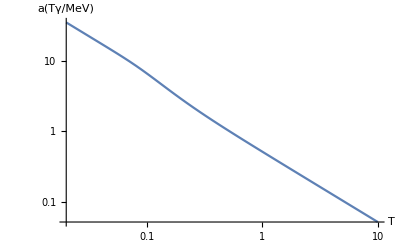

LogLogPlot::plln: Limiting value Log[t0] in {tt,Log[t0],Log[tmax]} is not a machine-sized real number.

LogLogPlot[aoftfunc[tt],{tt,t0,tmax},AxesLabel→{t(s),a(t/s)}]

LogLogPlot::plln: Limiting value Log[a0] in {aa,Log[a0],Log[amax]} is not a machine-sized real number.

LogLogPlot[Tγofafunc[aa],{aa,a0,amax},AxesLabel→{a,Tγ/MeV}]

LogLogPlot::plln: Limiting value Log[t0] in {tt,Log[t0],Log[tmax]} is not a machine-sized real number.

LogLogPlot[Tγoftfunc[tt],{tt,t0,tmax},AxesLabel→{t(s),Tγ/MeV}]

LogLogPlot::plln: Limiting value Log[t0] in {tt,Log[t0],Log[tmax]} is not a machine-sized real number.

LogLogPlot[TγTνoftfunc[tt],{tt,t0,tmax},AxesLabel→{t(s),Tγ/Tν}]

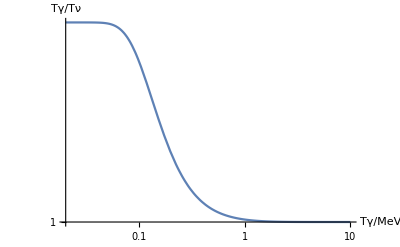

```mathematica
LogLogPlot[{zγofafunc[a],zνofafunc[a]},{a,a0,amax},AxesLabel->{"a","z"},PlotRange->All]

LogLogPlot[NaParthenope[a],{a,a0,amax},AxesLabel->{"a","N"}]

LogLogPlot[Hubbleofa[a],{a,a0,amax},AxesLabel->{"a","Mpl H /Tγ^2"}]

LogLogPlot[aofTγfunc[Tg],{Tg,10,0.02},AxesLabel->{"T","a(Tγ/MeV)"}]

LogLogPlot[aoftfunc[tt],{tt,t0,tmax},AxesLabel->{"t(s)","a(t/s)"}]

LogLogPlot[Tγofafunc[aa],{aa,a0,amax},AxesLabel->{"a","Tγ/MeV"}]

LogLogPlot[Tγoftfunc[tt],{tt,t0,tmax},AxesLabel->{"t(s)","Tγ/MeV"}]

LogLogPlot[TγTνoftfunc[tt],{tt,t0,tmax},AxesLabel->{"t(s)","Tγ/Tν"}]

LogLogPlot[TγTνofTγfunc[Tg],{Tg,10,0.02},AxesLabel->{"Tγ/MeV","Tγ/Tν"}]
```